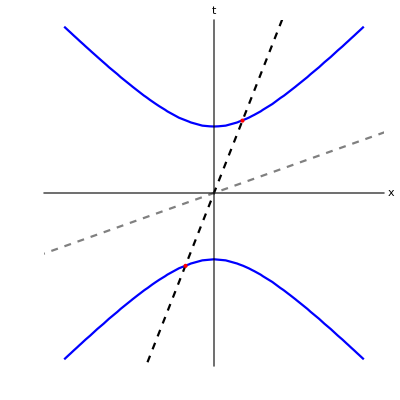

```mathematica
b=4;
Show[ContourPlot[-x^2/b^2+t^2/b^2==1,{x,-10,10},{t,-10,10},PerformanceGoal->"Quality", Axes->True, Frame->False, Ticks->None, AxesStyle->{{Thick, Arrowheads[{0.0,0.03}], Black
},{Thick, Arrowheads[{0.0,0.03}], Black}}, ContourStyle->Blue],Plot[2.5t, {t, -15, 15}, PlotStyle->{Dashed, Black}],Plot[.35t, {t, -15, 15}, PlotStyle->{Dashed,Gray}],Graphics[{PointSize[Medium], Red,Point[{1.74,4.35}]}],Graphics[{PointSize[Medium], Red,Point[{-1.74,-4.38}]}],AxesLabel->{Text[Style["x",15, Bold, FontFamily->"CMU Classical Serif"]],Text[Style[ToExpression["t",TeXForm,HoldForm],15, Bold ,FontFamily->"CMU Classical Serif"]]}, AspectRatio->Full]
```

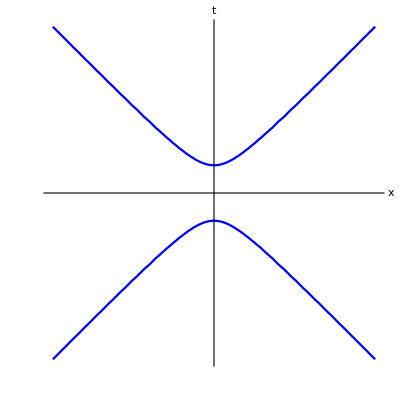

```mathematica
ContourPlot[-x^2/b^2+t^2/b^2==1,{x,-6,6},{t,-6,6},PerformanceGoal->"Quality", Axes->True, Frame->False, Ticks->None, AxesStyle->{{Thick, Arrowheads[{0.0,0.03}], Black},{Thick, Arrowheads[{0.0,0.03}], Black}},
AxesLabel->{Text[Style["x",15, Bold, FontFamily->"CMU Classical Serif"]],Text[Style[ToExpression["t",TeXForm,HoldForm],15, Bold ,FontFamily->"CMU Classical Serif"]]}, ContourStyle->Blue]
```

```mathematica
Export["Universidad/hyperbole.pdf",%];
```

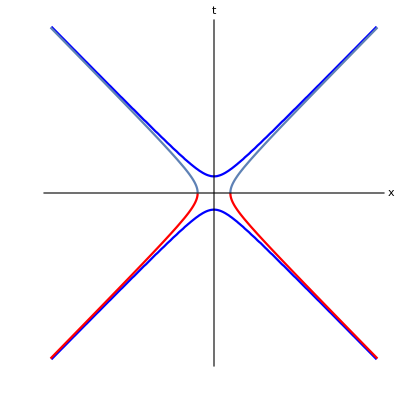

```mathematica
Show[ContourPlot[-x^2/b^2+t^2/b^2==1,{x,-10,10},{t,-10,10},PerformanceGoal->"Quality", Axes->True, Frame->False, Ticks->None, AxesStyle->{{Thick, Arrowheads[{0.0,0.03}], Black},{Thick, Arrowheads[{0.0,0.03}], Black}},
AxesLabel->{Text[Style["x",15, Bold, FontFamily->"CMU Classical Serif"]],Text[Style[ToExpression["t",TeXForm,HoldForm],15, Bold ,FontFamily->"CMU Classical Serif"]]}, ContourStyle->Blue],Plot[Sqrt[t^2-b^2],{t,-10, 10}],Plot[-Sqrt[t^2-b^2],{t,-10, 10}, PlotStyle->Red]]
```

```mathematica
Solve[v t == Sqrt[t^2-β^2],{t}]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{t→-β/(√(1-v^2))},{t→β/(√(1-v^2))}}

```mathematica
Export["Universidad/intersection.pdf",%];
```